### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=If[l==-1,1,If[l==0,#,ϕ[2^l(#-2^-l(2i-1))]]]&
ϕ[lx_,ly_,i_,j_]:=ϕ[lx,i][#1]ϕ[ly,j][#2]&
ψ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx i)]ϕ[2^ly(#2-2^-ly j)]&
ceil[x_,l_]:=If[x≥1,2^(l-1),1+Floor[2^(l-1)x]]
switch[x_]:=If[x≥1,x,1]
switch2[x_]:=If[x==-1,0,If[x==0,1,2^-x]]

column2[diag_,row_]:=If[diag<1,diag, If[row<1,diag,diag-row+1]]
column1[diag_,row_]:=If[diag==row,-1,column2[diag,row]]

getrow[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[perp,0],perp≤diag,perp,True,diag]
getcol[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[diag-perp,0],perp>0,diag-perp+1,True,diag]

endperp[n_]:=Which[n==-1,-1,n==0,1,True,n+2]

dϕ[x_]:=Which[Abs[x]>1,0,
			x==1 ,-1/2,
			x==-1,1/2,
			x==0,0,
			x>0,-1,
			True,1](* Don't think I need this*)
```

### Standard Basis

```mathematica
standardCoefficients2D[f_,lx_,ly_]:=Table[f[2^-lx i,2^-ly j],{i,0,2^lx},{j,0,2^ly}]
standardReconstruct2D[coefficients_,lx_,ly_]:=Sum[coefficients[[i+1,j+1]] ψ[lx,ly,i,j][#1,#2],{i,0,2^lx},{j,0,2^ly}]&

standardProject2D[f_,lx_,ly_]:=standardReconstruct2D[standardCoefficients2D[f,lx,ly],lx,ly]
```

### Full Basis

```mathematica
getCoefficient[f_,x_,l_]:=N@If[l==-1,f[0],If[l==0,f[1]-f[0],f[x]-1/2. f[x+2^-l]-1/2. f[x-2^-l]]]

getCoefficient2D[f_,x_,y_,lx_,ly_]:=getCoefficient[Function[y1,getCoefficient[Function[x1,f[x1,y1]],x,lx]],y,ly]
(* Tensor product construction
*)

fullCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^switch[kx]-1,2},{j,1,2^switch[ky]-1,2}],{kx,-1,lx},{ky,-1,ly}]


Reconstruct2D[coefficients_]:= Sum[coefficients[[kx+2,ky+2,ceil[#1,switch[kx]],ceil[#2,switch[ky]]]] 
ϕ[kx,ky,ceil[#1,switch[kx]],ceil[#2,switch[ky]]][#1,#2]
,{kx,-1,Length[coefficients]-2},{ky,-1,Length[coefficients]-2}]&

reverseFlatten[coefficients_,kx_,ky_]:=Module[{k},k=0;Return[Table[Table[coefficients[[++k]] ,{i,1,2^(switch[lx]-1)},{j,1,2^(switch[ly]-1)}],{lx,-1,kx},{ly,-1,ky}]];]


project2D[f_,lx_,ly_]:=Reconstruct2D[fullCoefficients2D[f,lx,ly]]
```

### Sparse Basis

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,switch2[getrow[perp,diag]] i,switch2[getcol[perp,diag]] j,getrow[perp,diag],getcol[perp,diag]],{i,1,2^switch[getrow[perp,diag]]-1,2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]

sparseReconstruct[coefficients_]:=Sum[Sum[coefficients[[diag+2,perp+2,ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]]] 
ϕ[getrow[perp,diag],getcol[perp,diag],ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]][#1,#2]
,{perp,-1,endperp[diag]}],{diag,-1,Length[coefficients]-2}]&

sparseProject[f_,n_]:=sparseReconstruct[sparseCoefficients2D[f,n]]

sparseIntegrate[f_,n_]:=Sum[Sum[Sum[f[switch2[getrow[perp,diag]]i,switch2[getcol[perp,diag]]j],{i,1,2^switch[getrow[perp,diag]]-1,2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]
```

### Differentiation

```mathematica
diffx[f_,l_]:=Which[#1< 2^-l,(f[#1+2^-l,#2]-f[#1,#2])/2^-l,#1> 1-2^-l,(f[#1,#2]-f[#1-2^(-l-1),#2])/2^-l,True,(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]&


diffy[f_,l_]:=
Which[#1< 2^-l,(f[#1+2^-l,#2]-f[#1,#2])/2^-l,#1> 1-2^-l,(f[#1,#2]-f[#1-2^-l,#2])/2^-l,True,(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]&
```

### Algorithms to form the D Matrices

```mathematica
dxMatrix[lx_,ly_]:=Flatten[Table[Table[fullCoefficients2D[diffx[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}],3]//Transpose
dyMatrix[lx_,ly_]:=Flatten[Table[Table[fullCoefficients2D[diffy[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}],3]//Transpose


dxMatrixStandard[lx_,ly_]:=Flatten[Table[standardCoefficients2D[diffx[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}],1]//Transpose
dyMatrixStandard[lx_,ly_]:=Flatten[Table[standardCoefficients2D[diffy[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}],1]//Transpose

(* SPARSE MATRICES HAVENT BEEN MADE YET *)
```

### Integration on the Grids

```mathematica
fullIntegrate[f_,kx_,ky_]:=Sum[2^-kx 2^-ky  posW[i,j] f[i,j],{i,0,1,2^-kx},{j,0,1,2^-ky}]
fullIntegrate[f_,kx_]:=Sum[2^-kx 2 posW[i,0]f[i],{i,0,1,2^-kx}]
sparseIntegrate[f_,n_]:=Sum[Sum[posW[i,j] 1/GCD[2^n i,2^(n)] 1/2^n f[i, j ],{j,0,1,1/GCD[2^n i,2^(n)]}],{i,0,1,2^(-n)}]
(*The area weights, although they sum to 1, are not totally right for sparse grids*)
```

### Algorithms to form the W Matrices

```mathematica
lagrangeW[lx_,ly_]:=Flatten[Table[Table[fullIntegrate[ψ[lx,ly,i1,j1][#1,#2] ψ[lx,ly,i2,j2][#1,#2]&,lx,ly],{i2,0,2^lx},{j2,0,2^ly}]//Flatten,{i1,0,2^lx},{j1,0,2^lx}],1]

fullW[lx_,ly_]:=Flatten[Table[Table[Table[Table[fullIntegrate[ϕ[kx1,ky1,i1,j1][#1,#2] ϕ[kx2,ky2,i2,j2][#1,#2]&,lx,ly],{i2,1,2^(switch[kx2]-1)},{j2,1,2^(switch[ky2]-1)}],{kx2,-1,lx},{ky2,-1,ly}]//Flatten,{i1,1,2^(switch[kx1]-1)},{j1,1,2^(switch[ky1]-1)}],{kx1,-1,lx},{ky1,-1,ly}],3]

fulldW[lx_,ly_]:=Flatten[Table[Table[Table[Table[fullIntegrate[ϕ[kx1,ky1,i1,j1][1,#] ϕ[kx2,ky2,i2,j2][1,#]-ϕ[kx1,ky1,i1,j1][0,#] ϕ[kx2,ky2,i2,j2][0,#]&,ly],{i2,1,2^(switch[kx2]-1)},{j2,1,2^(switch[ky2]-1)}],{kx2,-1,lx},{ky2,-1,ly}]//Flatten,{i1,1,2^(switch[kx1]-1)},{j1,1,2^(switch[ky1]-1)}],{kx1,-1,lx},{ky1,-1,ly}],3]
```

```mathematica
Table[#[[i,i]],{i,1,81}]&@lagrangeW[3,3]
```

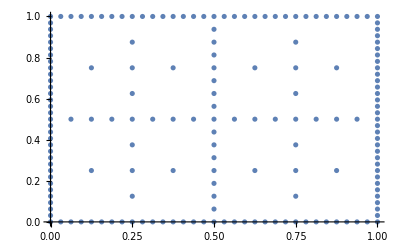

```mathematica
ListPlot[Flatten[Table[Table[{i, j },{j,0,1,1/GCD[2^5 i,2^(5)]}],{i,0,1,2^(-5)}],1]]
```

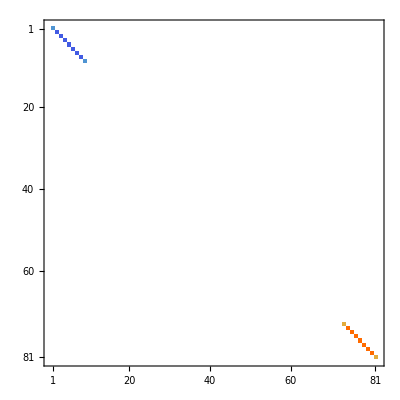

```mathematica
(#+Transpose@#)&@(dxMatrixStandard[3,3].lagrangeW[3,3])//MatrixPlot
```

```mathematica
(#+Transpose@#-fulldW[3,3])&@(dxMatrix[3,3].fullW[3,3])//MatrixPlot
```

-Graphics-